Happy numbers: https://www.youtube.com/watch?v=kC6YObu61_w
Melancoil: https://www.youtube.com/watch?v=_DpzAvb3Vk4

```mathematica
g=DeleteDuplicates[Flatten[Table[NestList[#[[2]]-> Total[IntegerDigits[#[[2]]]^2]&,{,i},20][[2;;-1]],{i,1,10000}]]];
```

```mathematica
endsIn[range_,exponent_,num_]:=DeleteDuplicates[Flatten[Select[Table[NestList[#[[2]]-> Total[IntegerDigits[#[[2]]]^exponent]&,{,i},20][[2;;-1]],{i,1,range}],#[[-1,2]]==num&]]];
```

```mathematica
melancoilN[range_,exponent_]:=Complement[DeleteDuplicates[Flatten[Table[NestList[#[[2]]-> Total[IntegerDigits[#[[2]]]^exponent]&,{,i},20][[2;;-1]],{i,1,range}]]],endsIn[range,exponent,1]]
```

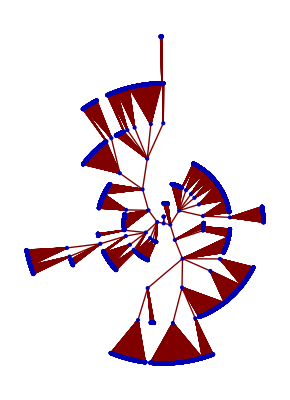

```mathematica
q=TreePlot[endsIn[100000,2,1],Center,LayerSizeFunction->(10#&),SelfLoopStyle->None,VertexLabeling->Tooltip]
```

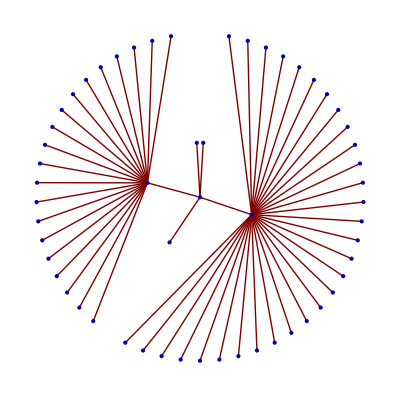

-Graphics-

```mathematica
vf[{xc_,yc_},name_,{w_,h_}]:=
Block[{xmin=xc-w,xmax=xc+w,ymin=yc-h,ymax=yc+h},
Polygon[{{xmin,ymin},{xmax,ymin},{xmax,ymax},{xmin,ymax}}]
];
```

```mathematica
w=Graph[endsIn[10000,3,1],VertexShapeFunction->vf,VertexLabels->Placed["Name",Tooltip]]
```

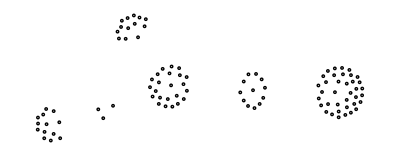

```mathematica
Graphics[Tooltip[Circle[5#,.25],#]&/@GraphEmbedding[w]]
```

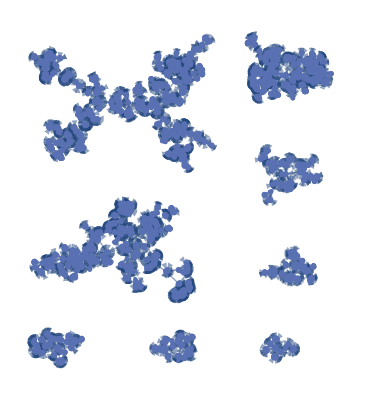

```mathematica
Graph[melancoilN[10000,3],VertexLabels->Placed["Name",Tooltip]]
```